# Five-point MRK plus near-planarity

## A simultaneous fixed-transverse multi-Regge and coplanar-limit audit

This notebook studies the two-loop six-edge fish topology in a composite limit in which both rapidity gaps become large while the transverse configuration approaches the coplanar boundary.  It places this limit on the same footing as the wide-angle near-planar and central-soft rapidity-ordered expansions.  All vectors are displayed as (v0,...,v5;1), including the expansion-parameter component.

## 1. Definition of the composite limit

We start from the exact on-shell light-cone chart used for general five-point kinematics.  The outgoing transverse momenta are p3_perp=q, p4_perp=k and p5_perp=-q-k.  Pp, Kp, Mm, Q2 and xi are fixed and positive.  Two independent positive integers a and b control the approach to planarity and the MRK rapidity growth, respectively.

{p3plus,p4plus,p5minus}=={Pp delta^-b,Kp,Mm delta^-b}

{k2,q2,twoqdotk}=={Q2,Q2 (1/xi^2+delta^(2 a)/4),(2 Q2)/xi}

{w,wbar}=={-1/xi+(ⅈ delta^a)/2,-1/xi-(ⅈ delta^a)/2}

Both rapidity gaps therefore scale in the standard fixed-transverse MRK manner.  Planarity is projective: the dimensionful Gram determinant contains the growing hard scale, but exactly Gamma5/s12^2=-Q2^2 delta^(2a).  It is this normalized quantity that tends to zero.

## 2. Topology, attachment and invariant stationary form

The graph is a theta graph with paths A=(x0,x1), B=(x2,x3), C=(x4,x5).  Its four-valent endpoint vertices are 3 and 5; vertices 1, 2 and 4 lie in the interiors of the three paths and are trivalent after attaching an external leg.  The calculation below uses external attachment order {1,2,3,5,4}: p3 and p4 occupy the four-valent endpoints, while the backward extremal parton p5 is attached to the trivalent vertex 4.  It is therefore not the rapidity-symmetric attachment.

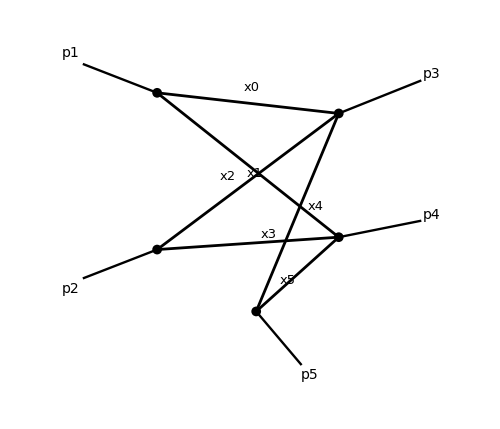

attachment order at vertices 1,...,5 | four-valent endpoints | location of p4 | positive stationary point?
{1,2,3,5,4} (representative) | {p3,p4} | endpoint 5 | yes
{1,2,4,5,3} (endpoint reflection) | {p4,p3} | endpoint 3 | yes
{1,2,3,4,5} (rapidity symmetric) | {p3,p5} | trivalent path vertex 4 | no

The distinction is dynamical, not presentational.  An exact scan of the twelve inequivalent attachment orders finds a positive stationary point only for the representative order and its endpoint reflection.  In the superficially natural rapidity-symmetric order {1,2,3,4,5}, the extremal partons p3 and p5 occupy the four-valent endpoints and p4 is emitted from the trivalent path vertex.  Its stationary ratios instead behave as

{rhoA,rhoB,rhoC} â.88.bc {-((Kp Mm xi) delta^-b)/Q2,((Kp (1+xi)) delta^b)/(Pp xi),-(1+xi)}

Two ratios are negative for all positive physical parameters, so this attachment has no positive first-sheet pinch on the coplanar MRK path.  The endpoint-reflected positive order has the same facet after x0<->x1, x2<->x3 and x4<->x5; its exceptional component is v3=b-2a rather than v2=b-2a.

Define qAB=s12-s34-s45, qBC=-s12-s23+s45 and qCA=s23.  The three stationary ratios rho solve the invariant linear system K rho=-ell.  With fA=x0-rhoA x1 and cyclic analogues, the exact massless polynomial is

F==qAB x5 fA fB+qBC x1 fB fC+qCA x3 fC fA+(Gamma5 x1 x3 x5)/(4 qAB qBC qCA)

The audit verifies this identity directly against the Symanzik polynomial in adjacent Mandelstam invariants.

## 3. The moving positive Landau locus

In this composite limit the stationary point is not fixed in projective Schwinger space.  Its ratios behave as

{rhoA,rhoB,rhoC} â.88.bc {xi,(Kp delta^b)/Pp,xi}

All three leading coefficients are positive for the physical parameter domain.  The middle ratio approaches a boundary at the MRK rate.  This moving Landau locus is the origin of the unequal x2 component in the final vector.

## 4. Local facet and cancellation layers

Introduce tangential coordinates uI and normal coordinates nI by

{x0,x1,x2,x3,x4,x5}=={rhoA uA+nA,uA,rhoB uB+nB,uB,rhoC uC+nC,uC}

The exact lower-facet scaling in these coordinates is

{uA,uB,uC,nA,nB,nC} â.88.bc {delta^(-2 a),delta^(-2 a),delta^(-2 a),delta^-a,delta^(-a+2 b),delta^-a}

Pulling this back to the original variables gives

vMRKPlanar=={-2 a,-2 a,b-2 a,-2 a,-2 a,-2 a,1}

The qAB and qBC sectors occur first at W=-6a-b and lose 2a+b powers through cancellation.  The qCA sector occurs at W=-6a and loses 2a powers.  Both reach WHR=-4a, where U and the Gram-normal term also enter.  Thus the equal-rate path has two cancellation layers, -7 and -6, before the resolved weight -4.

### Exact equal-rate certificate

original vector |     -2-2-1-2-2-21
local vector |     -2-2-2-11-11
leading monomials | 7
affine rank | 6
full lower facet | True
Gamma identity | True
invariant decomposition | True

The seven leading monomials span affine rank six in the six local variables.  This is the necessary full-dimensional lower-facet certificate; the result is not inferred merely from a candidate scaling vector.

### Parameter-space power count

For unit propagator powers, the six local measures contribute delta^(-9a+2b).  Since the resolved Lee-Pomeransky polynomial has weight -4a, its power -D/2 contributes delta^(2a D).  Therefore

IntegralScaling==delta^(-9 a+2 b+2 a D)

At equal rates and D=4-2 epsilon this is delta^(1-4 epsilon).  The epsilon-dependent exponent confirms that this is an infrared region even though the scalar integral is power suppressed in this dimensionful MRK chart.

### Momentum-space mode reconstruction

For the positive representative attachment the equal-rate Landau saddle has the following component valuations.  Exactly at the saddle every propagator has virtuality O(delta^2).  The Schwinger vector nevertheless requires q2^2=O(delta) across the local integration region, so this dependent edge has one additional cancellation precisely at the saddle; that fact alone does not compare a mode-adapted independent loop momentum with its width.

edge | central (plus, minus, transverse) | saddle q_e^2 power | region q_e^2 power
x0 |     3-11 | 2 | 2
x1 |     3-11 | 2 | 2
x2 |     -131 | 2 | 1
x3 |     031 | 2 | 2
x4 |     1-10 | 2 | 2
x5 |     1-10 | 2 | 2

-Graphics-

Dark green, olive and teal distinguish the three theta-path collinear flows A, B and C.  The displayed edge triples are central saddle values; the table separately records the region virtualities.  The blue external line is the fixed-transverse central parton p4, while the blue discs mark the two hard four-valent vertices that delimit the collinear paths.  Each collinear path mode keeps one shade throughout: A/p1 is dark green, B/p2,p3 is olive, and C/p5 is teal.  Although p1 and p5 approach the same backward direction in MRK, the A- and C-path momenta have distinct global-frame component scalings and are separated by hard interactions; they are therefore not assigned the same mode colour.  The outgoing legs are arranged top-to-bottom in their MRK rapidity order p3,p4,p5.  The crossing of the two lower external lines changes only the drawing, not the graph attachment.  There is no independent Glauber loop and therefore no Glauber vertex marker.  A path-adapted independent basis uses the A and C flows.  In their respective local lightcone frames both central values and marginal widths scale as (2a+b,-b,a), and each loop measure contributes delta^(a D).  Momentum conservation restricts their correlated longitudinal support by delta^(3a+b).

MomentumScaling==delta^(a D) delta^(a D) delta^(3 a+b) delta^(-(12 a-b))==delta^(-9 a+2 b+2 a D)

This exactly reproduces the parameter-space count.  The endpoint-reflected positive attachment is obtained by x0<->x1, x2<->x3 and x4<->x5; the path colours and absence of a Glauber loop are unchanged.

## 5. Dependence on the relative rates

The formula is stable when the two rates are varied.  The table evaluates the analytic support formula; the exact equal-rate row is independently reconstructed from the complete local Lee-Pomeransky polynomial above.

a | b | v=(v0,...,v5;1) | WHR | rank | facet?
1 | 1 |     -2-2-1-2-2-21 | -4 | 6 | True
1 | 2 |     -2-20-2-2-21 | -4 | 6 | True
2 | 1 |     -4-4-3-4-4-41 | -8 | 6 | True
1 | 3 |     -2-21-2-2-21 | -4 | 6 | True
2 | 3 |     -4-4-1-4-4-41 | -8 | 6 | True
3 | 1 |     -6-6-5-6-6-61 | -12 | 6 | True
3 | 2 |     -6-6-4-6-6-61 | -12 | 6 | True

## 6. Comparison of the three five-point paths

Expansion | Kinematic path | powers of (rhoA,rhoB,rhoC) | original-coordinate vector | cancellation weights
Near-planar wide angle | fixed wide-angle invariants | (0,0,0) | (-2,-2,-2,-2,-2,-2;1) | one symmetric cancellation level: -6 -> -4
MRK plus planarity (a=b=1) | two standard MRK gaps; fixed transverse scales | (0,1,0) | (-2,-2,-1,-2,-2,-2;1) | two levels: -7,-6 -> -4
Central-soft rapidity ordered | soft p4 transverse scale and asymmetric rapidity ordering | different two-factor locus | (-4,-4,-1,-4,-4,-4;1) | -9 -> -8

For the representative attachment, the simultaneous MRK-plus-planarity region is best viewed as a kinematic degeneration and reweighting of the same three-normal coplanar Landau family that produces its wide-angle Landshoff region.  It is not the central-soft region: the latter uses a different kinematic path and a different factorized cancellation locus.  Nor does the result extend to the rapidity-symmetric attachment, which fails positivity before the facet analysis.

## 7. Relation to the current HRF wrapper

The generic asymptotic-alignment scan exposes the relevant face, but presently harvests only a single product factor there.  Its staged composition then fails the facet test.  The exact three-normal local audit proves that this is a limitation of that wrapper, not absence of the region.  This notebook is therefore also a regression target for extending the general alignment-plus-harvest interface.

## 8. Reproducibility

The following cells load the stored exact results.  The second cell reruns the full symbolic equal-rate parameter audit; on Mathematica 15.0 it takes roughly one minute on the development machine.  The third reruns the exact momentum-mode and power-counting audit.

```mathematica
result = Get[FileNameJoin[{NotebookDirectory[], "results", "equal_rate_audit.wl"}]];
KeyTake[result, {"OriginalCoordinateRegionVector", "LayerWeights", "LeadingMonomialCount", "LeadingAffineRank", "FullLowerFacetCertificateQ"}]
```

```mathematica
$HRF5MRKPlanarLibraryOnly = True;
Get[FileNameJoin[{NotebookDirectory[], "HRF_FivePointMRKPlanarCompositeAudit.wl"}]];
exactEqualRateAudit = hrf5MRKPlanarAudit[1, 1];
```

```mathematica
$HRF5MRKPlanarMomentumAuditLibraryOnly = True;
Get[FileNameJoin[{NotebookDirectory[], "HRF_FivePointMRKPlanarMomentumAudit.wl"}]];
momentumAudit = hrf5MRKPlanarMomentumAudit[];
```